```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\shiyi\work\git\fluc_T\fluctuations_T\highorder_2p1\input_h\Tpc

### Lattice

```mathematica
HotQCDp=Flatten[Import["../../../LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["../../../LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["../../../LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["../../../LQCDdata/hotdpt4u.dat"]];
Tcl=1;
Hotpdown=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrup}];
WBp=Flatten[Import["../../../LQCDdata/wbpt4.dat"]];
WBdp=Flatten[Import["../../../LQCDdata/wbdpt4.dat"]];
WBT=Flatten[Import["../../../LQCDdata/wbT.dat"]];
WBdown=Transpose[{WBT/Tcl,WBp-WBdp}];
WBup=Transpose[{WBT/Tcl,WBp+WBdp}];
WBcs=Table[Import["../../../LQCDdata/WB-EoS.dat"][[i]][[-2]],{i,2,63}];
WBcserr=Table[Import["../../../LQCDdata/WB-EoS.dat"][[i]][[-1]],{i,2,63}];
WBcsup=Transpose[{WBT/Tcl,WBcs+WBcserr}];
WBcsdown=Transpose[{WBT/Tcl,WBcs-WBcserr}];
WBp2025=Flatten[Import["../../../LQCDdata/WB2025/PT4WB.dat"]];
WBdp2025=Flatten[Import["../../../LQCDdata/WB2025/PT4WB_erro.dat"]];
WBT2025=Flatten[Import["../../../LQCDdata/WB2025/TWB.dat"]];
WBdown2025=Transpose[{WBT2025/Tcl,WBp2025-WBdp2025}];
WBup2025=Transpose[{WBT2025/Tcl,WBp2025+WBdp2025}];
```

### Model

```mathematica
mub={0,100,200,300,400,500,550};
T=Table[i,{i,1,250}];
mfmub0=Transpose[{T,Transpose[Import["./mub0/TemB1/BUFFER/MF.DAT"]][[1]]}];
mfmub100=Transpose[{T,Transpose[Import["./mub100/TemB1/BUFFER/MF.DAT"]][[1]]}];
mfmub200=Transpose[{T,Transpose[Import["./mub200/TemB1/BUFFER/MF.DAT"]][[1]]}];
mfmub300=Transpose[{T,Transpose[Import["./mub300/TemB1/BUFFER/MF.DAT"]][[1]]}];
mfmub400=Transpose[{T,Transpose[Import["./mub400/TemB1/BUFFER/MF.DAT"]][[1]]}];
mfmub500=Transpose[{T,Transpose[Import["./mub500/TemB1/BUFFER/MF.DAT"]][[1]]}];
mfmub550=Transpose[{T,Transpose[Import["./mub550/TemB1/BUFFER/MF.DAT"]][[1]]}];
```

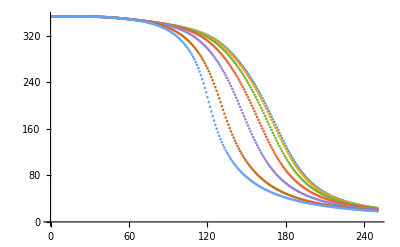

```mathematica
ListPlot[{mfmub0,mfmub100,mfmub200,mfmub300,mfmub400,mfmub500,mfmub550}]
```

```mathematica
dmfdTmub0=Table[-D[Interpolation[mfmub0][x],x][[0]][i],{i,1,250}];
dmfdTmub100=Table[-D[Interpolation[mfmub100][x],x][[0]][i],{i,1,250}];
dmfdTmub200=Table[-D[Interpolation[mfmub200][x],x][[0]][i],{i,1,250}];
dmfdTmub300=Table[-D[Interpolation[mfmub300][x],x][[0]][i],{i,1,250}];
dmfdTmub400=Table[-D[Interpolation[mfmub400][x],x][[0]][i],{i,1,250}];
dmfdTmub500=Table[-D[Interpolation[mfmub500][x],x][[0]][i],{i,1,250}];
dmfdTmub550=Table[-D[Interpolation[mfmub550][x],x][[0]][i],{i,1,250}];
```

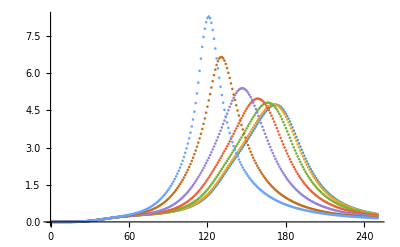

```mathematica
ListPlot[{dmfdTmub0,dmfdTmub100,dmfdTmub200,dmfdTmub300,dmfdTmub400,dmfdTmub500,dmfdTmub550}]
```

```mathematica
Export["mfmub0.dat",Transpose[mfmub0][[2]]];
Export["mfmub100.dat",Transpose[mfmub100][[2]]];
Export["mfmub200.dat",Transpose[mfmub200][[2]]];
Export["mfmub300.dat",Transpose[mfmub300][[2]]];
Export["mfmub400.dat",Transpose[mfmub400][[2]]];
Export["mfmub500.dat",Transpose[mfmub500][[2]]];
Export["mfmub550.dat",Transpose[mfmub550][[2]]];
```

```mathematica
Export["dmfdTmub0.dat",dmfdTmub0];
Export["dmfdTmub100.dat",dmfdTmub100];
Export["dmfdTmub200.dat",dmfdTmub200];
Export["dmfdTmub300.dat",dmfdTmub300];
Export["dmfdTmub400.dat",dmfdTmub400];
Export["dmfdTmub500.dat",dmfdTmub500];
Export["dmfdTmub550.dat",dmfdTmub550];
```

```mathematica
lmub0=Transpose[{T,Transpose[Import["./l.DAT"]][[1]]}];
dldTmub0=Table[D[Interpolation[lmub0][x],x][[0]][i],{i,1,250}];
```

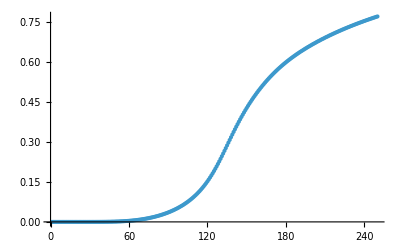

```mathematica
ListPlot[lmub0]
```

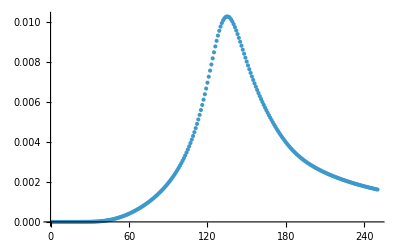

```mathematica
ListPlot[dldTmub0]
```

```mathematica
Export["dldTmub0.dat",dldTmub0];
```